```mathematica
logpRatio[sN_,r_,c_]:=If[r==c,(r+1)/r*(sN/2-r+1), sN*(r-1)/(r-c)+(sN*r*(c-1)-(1-r*c)*(r-c))/(c-r)^2*Log[c/r]]
logpRatio[sN,r,c]
```

If[r==c,((r+1) (sN/2-r+1))/r,(sN (r-1))/(r-c)+((sN r (c-1)-(1-r c) (r-c)) Log[c/r])/(c-r)^2]

```mathematica
logmRatio[sN_,r_,c_]:=If[r==c,(r+1)/r*(sN/2-r+1), sN*(r-1)/(r-c)+(1+(sN*r*(c-1)-(1-r*c)*(r-c))/(c-r)^2)*Log[c/r]]
```

```mathematica
plane=ContourPlot3D[sn==0,{c,0.5,2},{r,0.5,2},{sn,-1,2},AxesLabel->{"c","r","sM"}, ContourStyle->Directive[Black,Opacity[0.5]],ViewPoint->{-1.5,-5,1.5},BoxRatios->{1,1,0.8},NormalsFunction->None,Mesh->None,Axes->False,Boxed->False];
surf=ContourPlot3D[logpRatio[sn,r,c]==0,{c,0.5,2},{r,0.5,2},{sn,-1,2},AxesLabel->{"c","r","sM"},ContourStyle->Directive[Green,Opacity[0.8]],ViewPoint->{-1.5,-5,1.5},BoxRatios->{1,1,0.8},NormalsFunction->None,MeshStyle->Opacity[0.5],Axes->False,Boxed->False];
plot=Show[surf,plane];
plot=Rotate[plot,1 Degree]
```

-Graphics3D-

```mathematica
Export["3d_ratio_surface_nobox.png",%, ImageResolution->300,Background->None]
```

3d_ratio_surface_nobox.png

```mathematica
contourRegionPlot3D[region_,{x_,x0_,x1_},{y_,y0_,y1_},{z_,z0_,z1_},opts:OptionsPattern[]]:=Module[{reg,preds},reg=LogicalExpand[region&&x0≤x≤x1&&y0≤y≤y1&&z0≤z≤z1];
preds=Union@Cases[reg,_Greater|_GreaterEqual|_Less|_LessEqual,-1];
Show@Table[ContourPlot3D[Evaluate[Equal@@p],{x,x0,x1},{y,y0,y1},{z,z0,z1},RegionFunction->Function@@{{x,y,z},Refine[reg,p]&&Refine[!reg,!p]},opts],{p,preds}]]
```

```mathematica
gammaCoop[s_,d_]:=If[s==1&& d==0,0,2*d/(2*d-s+1)]
gammaComp[s_,d_]:=2*d/(s+1)
thikness=0.0075;
smallThickness=0.01;
```

```mathematica
bottomRegion=contourRegionPlot3D[z<0&&z-logpRatio[sN_,r_,c_][x,y]<0,{x,0,1},{y,0,1},{z,0,1},Mesh->{7,7,0},ContourStyle->Directive[Red,Opacity[0.7]],MeshStyle->Thickness[thikness],BoundaryStyle->Thickness[thikness]];
```

```mathematica
selfishness=Show[bottomRegion,Axes->False,ViewPoint->{-2,-4,1},Boxed->False]
```

-Graphics3D-

```mathematica
c[g1_,g2_]:=g1/g2
s[g1_,g2_,g0_]:=g0/g1/g2*(g1-g2)
r[a_,g1_,g2_]:=a*g1/g2
logRatioChem[g1_,g2_,g0_,M_]:=logpRatio[s[g1,g2,g0]*M/g2,c[g1,g2],c[g1,g2]]
```

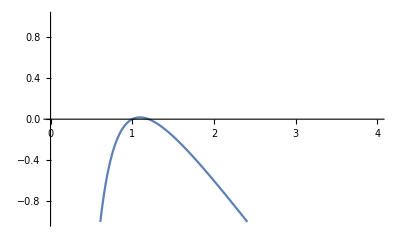

```mathematica
aa=1;
MM=200;
gg0=0.012;
gg2=1;
Plot[logRatioChem[g1,gg2,gg0,aa,MM],{g1,0.1,4},PlotRange->{-1,1}]
```

```mathematica
logRatioChem[g1,g2,g0,M]
dg=Simplify[D[logRatioChem[g1,g2,g0,M],g1]]
```

((1+g1/g2) g2 (1-g1/g2+(g0 (g1-g2) M)/(2 g1 g2^2)))/g1

-1/g2-g2/g1^2+(g0 M)/g1^3

```mathematica
Reduce[dg==0&&g1>0&&g2>0&&g0>0&&M>0,g1]
```

M>0&&g2>0&&g0>0&&g1==Root[-g0 g2 M+g2^2 #1+#1^3&,1]

```mathematica
#1
```

#1

```mathematica
Reduce[(dg/.{g2->1.0948229420329678,M->200,g0->0.012})==0&&g1>0,g1]
```

g1==1.09545